```mathematica
ClearAll["Global`*"]
```

## Input Data

```mathematica
({20.538281602919813,36.40238371990682,54.53259112896524,65.86401567212864,86.26063532022391,99.99940391390135,95.32582650118889,50.000000000000014,45.46740887103481,38.66857084053389,34.135984327872855}+{22.804651078533837,38.66857084053389,54.53259112896524,68.13029746478783,93.05944316664879,97.59210117596801,81.72807345879262,63.597615876712766,38.66857084053389,38.66857084053389,38.66857084053389})/2
```

{21.6715,37.5355,54.5326,66.9972,89.66,98.7958,88.5269,56.7988,42.068,38.6686,36.4023}

```mathematica
Pup={13.739364679776209,38.66857084053389,47.7337089234288,72.66275122347781,97.59210117596801,99.99940391390135,90.79321059510724,68.13029746478783,52.266291076609924,18.271927482405022,22.804651078533837}/100;

ϕdet = 0;
ϕstep = 2π/10;
ϕdat = Table[ϕdet  + i ϕstep,{i,0,10}];

data  = Transpose[{ϕdat, Pup }];
A0approx = 1;
```

## Functions

```mathematica
FitFunc[A_, ϕ0_, ϕvar_, B_] := A/2 (Sin[ϕvar + ϕ0] - 1/3) + 2/3 ;
fit=NonlinearModelFit[data,{FitFunc[A0,ϕ0,ϕvar, B], A0 < 1},{{A0,A0approx},{ϕ0,0}, {B}},ϕvar]
```

FittedModel[2/3+0.363483 (-1/3-Sin[1.49133-ϕvar])]

## Output

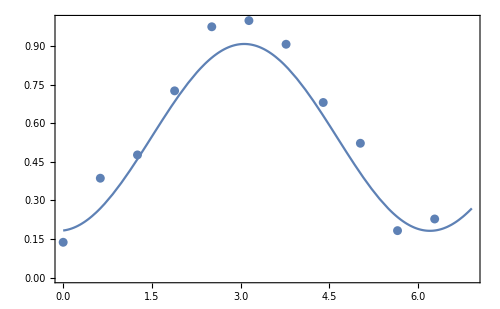

```mathematica
Show[ListPlot[data],
Plot[fit["BestFit"]/.ϕvar-> ϕ, {ϕ,ϕdet, ϕdet + 11 ϕstep}],
PlotRange-> {{ϕdet, ϕdet + 11 ϕstep},{0,1}},
Frame-> True, ImageSize-> 500]
```

```mathematica
fit["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
A0 | 0.726966 | 0.0663141 | 10.9625 | 4.25732×10^-6
ϕ0 | -1.49133 | 0.114448 | -13.0306 | 1.14158×10^-6
B | 1. | 0. | ∞ | 0.

## Exponential Decay Fit

```mathematica
Needs["ErrorBarPlots`"]
```

FittedModel[ⅇ^(-5.58715×10^-9 tvar^3)]

| Estimate | Standard Error | t-Statistic | P-Value
Γ | 563.555 | 18.8586 | 29.8831 | 7.87002×10^-7
α | 2. | 0. | ∞ | 0.

ⅇ^(-5.58715×10^-9 tvar^3)

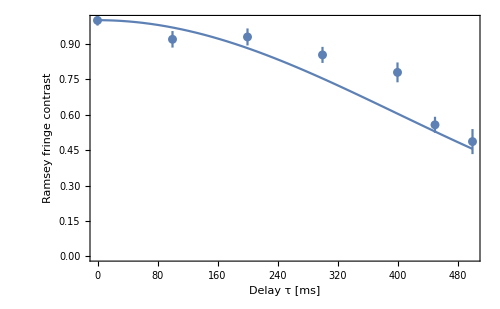

```mathematica
decaydata = {{0,0.999},{100, 0.919},{200, 0.929 }, {300, 0.853}, {400, 0.779},{450,0.557},{500,0.486}};
decaydataPlot = {{{0,0.999}, ErrorBar[0.022]},{{100, 0.919},ErrorBar[0.035]},{{200, 0.929},ErrorBar[0.036]},{{300, 0.853},ErrorBar[0.034]},{{400, 0.779},ErrorBar[0.042]},{{450, 0.557},ErrorBar[0.034]},{{500, 0.486},ErrorBar[0.053]}};

(*decayfunc[tvar_, Γ_] := Exp[-tvar/Γ];*)
decayfunc[tvar_, Γ_, α_] := Exp[-(tvar/Γ)^3];
decayfit = NonlinearModelFit[decaydata,decayfunc[tvar, Γ, α],{{Γ,1500}, {α, 2}},tvar]
decayfit["ParameterTable"]
decayfit["BestFit"]
Show[ErrorListPlot[decaydataPlot],
Plot[(Exp[-(tvar^α/Γ^α)]/.decayfit["BestFitParameters"])/.tvar-> t, {t, 0, 500}],
PlotRange-> {{0, 500},{0,1}},
Frame-> True, ImageSize-> 500, AxesOrigin-> False, FrameLabel->{{"Ramsey fringe contrast",Null},{"Delay τ [ms]","Coherence time (T2) = 0.84(71) s" }}, LabelStyle-> 15]
```

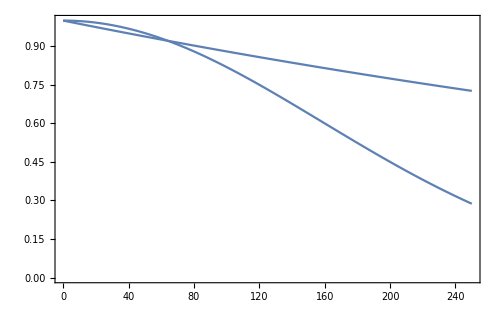

```mathematica
Show[Plot[Exp[-0.001278 t], {t, 0, 250}] ,
Plot[ Exp[-10^-4.7 t^2], {t, 0, 250}] ,
Frame-> True, ImageSize-> 500, AxesOrigin-> False, PlotRange-> {{0, 250},{0,1}}]
```

```mathematica
Plot[Exp[-10^-6 t^2], {t, 0, 250}PlotRange-> {{0, 250},{0,1}}]
```

Plot::pllim: Range specification {PlotRange t,0,250 PlotRange}→{{0,250},{0,1}} is not of the form {x, xmin, xmax}.

Plot[Exp[-t^2/10^6],{t,0,250} PlotRange→{{0,250},{0,1}}]

## Multiple Ramsey Fringe Plot

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
{8.33322554835588,8.33322554835588,23.684344691143288,63.15778989888299,85.08773731983001,89.47369483804155,82.89473073533648,63.15778989888299,49.99999999999999,30.263166228310283,17.10526926466357} + {17.10526926466357,34.64913020007265,25.87719717284908,56.5789820645065,85.08773731983001,99.99940391390135,82.89473073533648,80.70158919399931,43.42101793547684,28.070296444509108,21.491124792523536}  
%/2
```

{25.4385,42.9824,49.5615,119.737,170.175,189.473,165.789,143.859,93.421,58.3335,38.5964}

{12.7192,21.4912,24.7808,59.8684,85.0877,94.7365,82.8947,71.9297,46.7105,29.1667,19.2982}

```mathematica
data0 = {0.000596086098654914,6.140341275839439,35.197373816823216,68.09208642610085,92.76308497545713,99.99940391390135,93.8596587241604,60.41660413610198,33.552643588831614,11.074551511391094,0.000596086098654914}/100;
data100 = {0.9873185498598003,12.170995760386269,45.065806911565204,69.73683631353941,88.37715657880395,99.01268145013991,87.82899977917688,63.706133894109996,34.64910008660216,12.17105731426352,14.583629573565487}/100;
data200 = {2.8509762878380913,18.20175116738878,33.552687969547115,58.77192144169871,93.85964425524986,99.12246792406862,94.73654937597145,64.25434280999858,40.13157509517745,20.39480697790343,7.2368343243824285}/100;
data300 = {13.815732347200829,12.719283921049115,40.13151652144501,63.15778989888299,93.85964425524986,93.8596587241604,85.0878248295603,65.3508163911402,42.32461243226187,14.91223563944774,13.815732347200829}/100;
data400 = {12.719247406509725,21.491177874214266,24.780770931996184,59.86838598169474,85.08773731983001,94.73654937597145,82.89473073533648,71.92968954644115,46.71050896773842,29.166731336409697,19.298197028593552}/100;
data500 = {24.780788517154956,30.263166228310283,54.385983455365846,64.25444715653202,70.83324764222698,81.79822720027103,79.6052322007379,57.675443050086216,55.48252298654603,46.71050896773842,31.359703441816514}/100

ϕdet = 0;
ϕstep = 2π/10;
ϕdat = Table[ϕdet  + i ϕstep,{i,0,10}];

dat0  = Transpose[{ϕdat, data0 }];
dat100  = Transpose[{ϕdat, data100 }];
dat200  = Transpose[{ϕdat, data200 }];
dat300  = Transpose[{ϕdat, data300 }];
dat400  = Transpose[{ϕdat, data400 }];
dat500  = Transpose[{ϕdat, data500 }];

data0 = Table[{dat0⟦i⟧, ErrorBar[Sqrt[(Abs[dat0⟦i⟧⟦2⟧ - (1 - dat0⟦i⟧⟦2⟧)])/200]]}, {i, 1, 11}]
data100 = Table[{dat100⟦i⟧, ErrorBar[Sqrt[(Abs[dat0⟦i⟧⟦2⟧ - (1 - dat0⟦i⟧⟦2⟧)])/200]]}, {i, 1, 11}];
data200 = Table[{dat200⟦i⟧, ErrorBar[Sqrt[(Abs[dat0⟦i⟧⟦2⟧ - (1 - dat0⟦i⟧⟦2⟧)])/100]]}, {i, 1, 11}];
data300 = Table[{dat300⟦i⟧, ErrorBar[Sqrt[(Abs[dat0⟦i⟧⟦2⟧ - (1 - dat0⟦i⟧⟦2⟧)])/100]]}, {i, 1, 11}];
data400 = Table[{dat400⟦i⟧, ErrorBar[Sqrt[(Abs[dat0⟦i⟧⟦2⟧ - (1 - dat0⟦i⟧⟦2⟧)])/100]]}, {i, 1, 11}];
data500 = Table[{dat500⟦i⟧, ErrorBar[Sqrt[(Abs[dat0⟦i⟧⟦2⟧ - (1 - dat0⟦i⟧⟦2⟧)])/100]]}, {i, 1, 11}];

FitFunc[A_, ϕ0_, ϕvar_] := A/2 (Sin[ϕvar + ϕ0] - 1/3) + 2/3;
A0approx = 1;
fit0=NonlinearModelFit[dat0,{FitFunc[A0,ϕ0,ϕvar], A0 < 1},{{A0,A0approx},{ϕ0,0}},ϕvar];
fit100=NonlinearModelFit[dat100,{FitFunc[A0,ϕ0,ϕvar], A0 < 1},{{A0,A0approx},{ϕ0,0}},ϕvar];
fit200=NonlinearModelFit[dat200,{FitFunc[A0,ϕ0,ϕvar], A0 < 1},{{A0,A0approx},{ϕ0,0}},ϕvar];
fit300=NonlinearModelFit[dat300,{FitFunc[A0,ϕ0,ϕvar], A0 < 1},{{A0,A0approx},{ϕ0,0}},ϕvar];
fit400=NonlinearModelFit[dat400,{FitFunc[A0,ϕ0,ϕvar], A0 < 1},{{A0,A0approx},{ϕ0,0}},ϕvar];
fit500=NonlinearModelFit[dat500,{FitFunc[A0,ϕ0,ϕvar], A0 < 1},{{A0,A0approx},{ϕ0,0}},ϕvar];
```

{0.247808,0.302632,0.54386,0.642544,0.708332,0.817982,0.796052,0.576754,0.554825,0.467105,0.313597}

{{{0,5.96086×10^-6},ErrorBar[0.0707103]},{{π/5,0.0614034},ErrorBar[0.0662266]},{{(2 π)/5,0.351974},ErrorBar[0.0384742]},{{(3 π)/5,0.680921},ErrorBar[0.0425348]},{{(4 π)/5,0.927631},ErrorBar[0.0653935]},{{π,0.999994},ErrorBar[0.0707103]},{{(6 π)/5,0.938597},ErrorBar[0.0662266]},{{(7 π)/5,0.604166},ErrorBar[0.0322748]},{{(8 π)/5,0.335526},ErrorBar[0.0405553]},{{(9 π)/5,0.110746},ErrorBar[0.0623903]},{{2 π,5.96086×10^-6},ErrorBar[0.0707103]}}

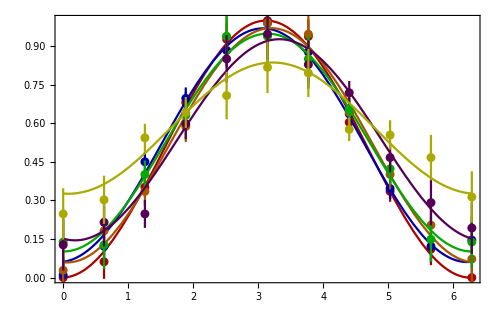

```mathematica
Show[ErrorListPlot[data0, PlotStyle-> {Darker[Red]}],
Plot[FitFunc[A0, ϕ0, ϕ]/.fit0["BestFitParameters"], {ϕ, 0, 2π}, PlotStyle-> {Darker[Red]}],
ErrorListPlot[data100, PlotStyle-> {Darker[Blue]}],
Plot[FitFunc[A0, ϕ0, ϕ]/.fit100["BestFitParameters"], {ϕ, 0, 2π}, PlotStyle-> {Darker[Blue]}],
ErrorListPlot[data200, PlotStyle-> {Darker[Orange]}],
Plot[FitFunc[A0, ϕ0, ϕ]/.fit200["BestFitParameters"], {ϕ, 0, 2π},PlotStyle-> {Darker[Orange]}],
ErrorListPlot[data300, PlotStyle-> {Darker[Green]}],
Plot[FitFunc[A0, ϕ0, ϕ]/.fit300["BestFitParameters"], {ϕ, 0, 2π}, PlotStyle-> {Darker[Green]}],
ErrorListPlot[data400, PlotStyle-> {Darker[Purple]}], 
Plot[FitFunc[A0, ϕ0, ϕ]/.fit400["BestFitParameters"], {ϕ, 0, 2π}, PlotStyle-> {Darker[Purple]}],
ErrorListPlot[data500, PlotStyle-> {Darker[Yellow]}], 
Plot[FitFunc[A0, ϕ0, ϕ]/.fit500["BestFitParameters"], {ϕ, 0, 2π}, PlotStyle-> {Darker[Yellow]}],
PlotRange-> {{0, 2π},{0,1}},
Frame-> True, ImageSize-> 500]
```